# Plot of temporal dynamics

## Plotting parameters [ENTER]

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{50,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.15,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

## Life-cycle [do not need if unchanged]

### Haploid competition

Frequency of haploids from each sex

```mathematica
Subscript[freqHap, sex_]:=ParallelSum[Subscript[fHap, x,y,z,sex],{x,{XZ,YW}},{y,{A,a}},{z,{M,m}}]
```

Mean haploid fitness of gametes from each sex

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{XZ,YW}},{y,{A,a}},{z,{M,m}}]/Subscript[freqHap, sex]
```

Frequencies of haploid genotypes from each sex following haploid competition, which occurs between gametes coming from the same sex

```mathematica
Subscript[fHapSel, x_,y_,z_,sex_]:=(Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex])/(Subscript[wbarHap, sex] Subscript[freqHap, sex])
```

### Random mating

Gametes from the two sexes pair at random

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,hom] Subscript[fHapSel, xP,yP,zP,het]
```

### Sex determination

Determine the sex of newly formed diploids

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become one heterogametic or homogametic

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,het]->1-Subscript[psex, zM,xP,zP,hom];
```

Rules for invasion of a dominant modifier into an XY (or ZW) system

```mathematica
invXY={
Subscript[psex, M,YW,M,hom]->0,(*always heterogametic sex if neo-SD allele wildtype (M) and have Y or W (YW) from heterogametic parent*)
Subscript[psex, M,XZ,M,hom]->1,(*always homogametic sex if neo-SD allele wildtype (M) and have X or Z from (XZ) heterogametic parent*)
Subscript[psex, m,xP_,zP_,hom]->k,(*ancestrally homogametic sex with probability k if mutation at the neo-SD locus (m) from homogametic parent*)
Subscript[psex, zM_,xP_,m,hom]->k (*ancestrally homogametic sex with probability k if mutation at the neo-SD locus (m) from heterogametic parent*)
};
```

### Diploid selection

Frequencies of diploids from each sex

```mathematica
Subscript[freqDip, sex_]:=ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]
```

Mean diploid fitness in each sex

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/Subscript[freqDip, sex]
```

Frequencies of diploid genotypes in each sex following diploid selection, which occurs separately in each sex (even if diploid selection is not direct competition between members of the same sex but instead viability selection, selection still effectively occurs ‘separately in each sex’ because the next generation is sired by 50% heterogametic sex and 50% homogametic sex)

```mathematica
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=(Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex])/(Subscript[wbarDip, sex] Subscript[freqDip, sex])
```

### Meiosis

Gamete genotypes produced by diploids

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,A,z1_]->Subscript[α, het](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,a,z2_]->(1-Subscript[α, het])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,A,z1_]->Subscript[α, het] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,a,z2_]->(1-Subscript[α, het])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,A,z2_]->Subscript[α, het] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,a,z1_]->(1-Subscript[α, het])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,A,z2_]->Subscript[α, het] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,a,z1_]->(1-Subscript[α, het])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,A,z2_]->Subscript[α, het] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,a,z1_]->(1-Subscript[α, het])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,A,z2_]->Subscript[α, het] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,a,z1_]->(1-Subscript[α, het])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,A,z1_]->Subscript[α, het] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,a,z2_]->(1-Subscript[α, het])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,A,z1_]->Subscript[α, het] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,a,z2_]->(1-Subscript[α, het]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,A,z1_]->Subscript[α, hom](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,a,z2_]->(1-Subscript[α, hom])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,A,z1_]->Subscript[α, hom] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,a,z2_]->(1-Subscript[α, hom])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,A,z2_]->Subscript[α, hom] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,a,z1_]->(1-Subscript[α, hom])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,A,z2_]->Subscript[α, hom] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,a,z1_]->(1-Subscript[α, hom]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,A,z2_]->Subscript[α, hom] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,a,z1_]->(1-Subscript[α, hom])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,A,z2_]->Subscript[α, hom] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,a,z1_]->(1-Subscript[α, hom])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,A,z1_]->Subscript[α, hom] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,a,z2_]->(1-Subscript[α, hom])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,A,z1_]->Subscript[α, hom] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,a,z2_]->(1-Subscript[α, hom]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements of loci

Let the probability of recombination (an odd number of cross-overs) between loci A and X be r, the probability of recombination between A and M be R, and the probability of recombination between X and M be χ.

We can then write, in general,

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

and for specific orders of loci we can substitute in the value of χ (alternatively one could do the same for R or r)

```mathematica
χXAM=χ->R(1-r)+r(1-R);
χXMA=χ->(r-R)/(1-2R);
χAXM=χ->(R-r)/(1-2r);
```

## Recursions [ENTER]

### Ancestral XY system

#### Find equilibrium frequencies of genotypes in each sex

```mathematica
freqsub={
Subscript[fHap, XZ,A,M,hom]->XAf,Subscript[fHap, XZ,a,M,hom]->Xaf,Subscript[fHap, XZ,A,m,hom]->XAwf,Subscript[fHap, XZ,a,m,hom]->Xawf,
Subscript[fHap, YW,A,M,hom]->YAf,Subscript[fHap, YW,a,M,hom]->Yaf,Subscript[fHap, YW,A,m,hom]->YAwf,Subscript[fHap, YW,a,m,hom]->Yawf,
Subscript[fHap, XZ,A,M,het]->XAm,Subscript[fHap, XZ,a,M,het]->Xam,Subscript[fHap, XZ,A,m,het]->XAwm,Subscript[fHap, XZ,a,m,het]->Xawm,
Subscript[fHap, YW,A,M,het]->YAm,Subscript[fHap, YW,a,M,het]->Yam,Subscript[fHap, YW,A,m,het]->YAwm,Subscript[fHap, YW,a,m,het]->Yawm
};
```

```mathematica
varsub={
Subscript[wDip, A,A,hom]->FAA,Subscript[wDip, A,a,hom]->FAa,Subscript[wDip, a,A,hom]->FAa,Subscript[wDip, a,a,hom]->Faa,Subscript[wDip, A,A,het]->MAA,Subscript[wDip, A,a,het]->MAa,Subscript[wDip, a,A,het]->MAa,Subscript[wDip, a,a,het]->Maa,Subscript[wHap, A,het]->MA,Subscript[wHap, a,het]->Ma,Subscript[wHap, A,hom]->FA,Subscript[wHap, a,hom]->Fa,Subscript[α, het]->MdA,Subscript[α, hom]->FdA
};
```

```mathematica
(*differenceEqs={
Subscript[fHapNext, XZ,A,M,hom]-Subscript[fHap, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom]-Subscript[fHap, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,M,het]-Subscript[fHap, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het]-Subscript[fHap, XZ,a,M,het],
Subscript[fHapNext, YW,A,M,het]-Subscript[fHap, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het]-Subscript[fHap, YW,a,M,het]
}/.Subscript[fHap, x_,y_,m,sex_]->0/.
Subscript[fHap, YW,y_,M,hom]->0/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.freqsub/.varsub/.recGen//Simplify*)
```

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=
equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA]=
{XAf,Xaf,XAm,Xam,YAm,Yam}/.NSolve[{(FA XAf (FAa Ma (FdA-XAf) Xam-FAA MA (-1+XAf) XAm)-Fa Xaf (Faa Ma XAf Xam+FAa MA (-FdA+XAf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),-(FA XAf (FAa Ma (-1+FdA+Xaf) Xam+FAA MA Xaf XAm)+Fa Xaf (Faa Ma (-1+Xaf) Xam+FAa MA (-1+FdA+Xaf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),(FA XAf (-2 Ma MAa (MdA (-1+r)+XAm) Yam+MA MAA (1-2 XAm) YAm)-2 Fa Xaf (Ma Maa XAm Yam+MA MAa (-MdA r+XAm) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(Fa Xaf (Ma Maa (1-2 Xam) Yam+2 MA MAa (1+MdA (-1+r)-r-Xam) YAm)-2 FA XAf (Ma MAa ((-1+MdA) r+Xam) Yam+MA MAA Xam YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(FA XAf (2 Ma MAa Yam (MdA r-YAm)+MA MAA (1-2 YAm) YAm)-2 Fa Xaf YAm (Ma Maa Yam+MA MAa (MdA (-1+r)+YAm)))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(-2 FA XAf Yam (Ma MAa (-1+MdA+r-MdA r+Yam)+MA MAA YAm)+Fa Xaf (Ma Maa (1-2 Yam) Yam-2 MA MAa ((-1+MdA) r+Yam) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm)))}=={0,0,0,0,0,0},{XAf,Xaf,XAm,Xam,YAm,Yam}]
```

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=
sieve[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA]=
Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==6,write=Append[write,eq[[i]]]]];
Sort[write]]
```

#### Next female X genotypes

```mathematica
(*Simplify[{
Subscript[fHapNext, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,m,hom],
Subscript[fHapNext, XZ,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(2 Fa FAa FdA MA (-(-1+r) XAm Yaf+k (r Xawf YAm-R ((-1+r) XAwm Yaf+r Xawf YAm)-(-1+R) XAm (Xawf+Yawf-r Yawf))+Xaf (XAm+k R (XAwm+r YAwm)))+FA (2 FAa FdA Ma (r Xam YAf+k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+XAf (Xam-k (-1+R) (Xawm+Yawm-r Yawm)))+FAA MA (XAm YAf+k (-(-r-R+2 r R) (XAwm YAf+XAwf YAm)+XAm (XAwf+YAwf-r YAwf-R YAwf+2 r R YAwf))+XAf (2 XAm+k (XAwm+YAwm-r YAwm-R YAwm+2 r R YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(-2 FA FAa (-1+FdA) Ma (-(-1+r) Xam YAf+k (r XAwf Yam-R ((-1+r) Xawm YAf+r XAwf Yam)-(-1+R) Xam (XAwf+YAwf-r YAwf))+XAf (Xam+k R (Xawm+r Yawm)))+Fa (Faa Ma (Xam Yaf+k (-(-r-R+2 r R) (Xawm Yaf+Xawf Yam)+Xam (Xawf+Yawf-r Yawf-R Yawf+2 r R Yawf))+Xaf (2 Xam+k (Xawm+Yawm-r Yawm-R Yawm+2 r R Yawm)))-2 FAa (-1+FdA) MA (r XAm Yaf+k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+Xaf (XAm-k (-1+R) (XAwm+YAwm-r YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(k (2 Fa FAa FdA MA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 FAa FdA Ma (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+FAA MA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(k (-2 FA FAa (-1+FdA) Ma (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Faa Ma (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 FAa (-1+FdA) MA (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next male X genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het],
Subscript[fHapNext, XZ,A,m,het],
Subscript[fHapNext, XZ,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(-2 Fa MA MAa MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+(-1+k) XAm (XAwf+(1-R+r (-1+2 R)) YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(2 FA Ma MAa (-1+MdA) (r (XAf+XAwf-k XAwf) Yam+(-1+k) (-1+R) Xam (XAwf+YAwf-r YAwf)+(-1+k) R ((-1+r) Xawm YAf+r XAwf Yam-XAf (Xawm+r Yawm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+(-1+k) Xam (Xawf+(1-R+r (-1+2 R)) Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))+(-1+k) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=((-1+k) (2 Fa MA MAa MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+MA MAA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=((-1+k) (-2 FA Ma MAa (-1+MdA) (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Ma Maa (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 MA MAa (-1+MdA) (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next female Y genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,hom],
Subscript[fHapNext, YW,a,M,hom],
Subscript[fHapNext, YW,A,m,hom],
Subscript[fHapNext, YW,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FA (-2 FAa FdA Ma ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+FAA MA (XAm (YAf+k (r+R-2 r R) YAwf)+k ((1-R+r (-1+2 R)) XAwm YAf+(1-r-R+2 r R) XAwf YAm+YAm YAwf+r XAf YAwm+R XAf YAwm-2 r R XAf YAwm+YAf YAwm)))+2 Fa FAa FdA MA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(-2 FA FAa (-1+FdA) Ma (k (XAwf (Yam-R Yam)+Yam (YAwf-R YAwf)+R (XAf+YAf) Yawm)+r (Xam (YAf-k (-1+R) YAwf)+k (-XAwf Yam+R (Xawm YAf+XAwf Yam-XAf Yawm))))+Fa (Faa Ma (Xam (Yaf+k (r+R-2 r R) Yawf)+k ((1-R+r (-1+2 R)) Xawm Yaf+(1-r-R+2 r R) Xawf Yam+Yam Yawf+r Xaf Yawm+R Xaf Yawm-2 r R Xaf Yawm+Yaf Yawm))+2 FAa (-1+FdA) MA ((-1+r) XAm (Yaf+k R Yawf)-k ((-1+r) (-1+R) XAwm Yaf+r R Xawf YAm+R YAm Yawf+r Xaf YAwm-r R Xaf YAwm+Yaf YAwm-R Yaf YAwm))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(k (-2 Fa FAa FdA MA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (-2 FAa FdA Ma (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+FAA MA (XAm YAwf+XAwm YAwf+YAm YAwf+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(k (2 FA FAa (-1+FdA) Ma (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Faa Ma (Xam Yawf+Xawm Yawf+Yam Yawf+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 FAa (-1+FdA) MA (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next male Y genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het],
Subscript[fHapNext, YW,A,m,het],
Subscript[fHapNext, YW,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(FA (2 Ma MAa MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm)))+MA MAA ((-1+k) (1-R+r (-1+2 R)) XAwm YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm-2 YAf YAm-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf-YAf YAwm+k YAf YAwm-XAf (YAm+(-1+k) (-r-R+2 r R) YAwm)))+2 Fa MA MAa MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(-2 FA Ma MAa (-1+MdA) (-XAf Yam-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam-YAf Yam-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf-R XAf Yawm+k R XAf Yawm-R YAf Yawm+k R YAf Yawm+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa ((-1+k) (1-R+r (-1+2 R)) Xawm Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam-2 Yaf Yam-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf-Yaf Yawm+k Yaf Yawm-Xaf (Yam+(-1+k) (-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) (-1+r) (-1+R) XAwm Yaf-Yaf YAm-R XAm Yawf+k R XAm Yawf-R YAm Yawf+k R YAm Yawf-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-r (-(-1+k) R (Xawf YAm-XAm Yawf)+Xaf (YAm+(-1+k) (-1+R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=-((-1+k) (2 Fa MA MAa MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (2 Ma MAa MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+MA MAA (-XAm YAwf-XAwm YAwf-YAm YAwf-XAf YAwm-XAwf YAwm-YAf YAwm-2 YAwf YAwm+r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)+R (-XAwm YAf-XAwf YAm+XAm YAwf+XAf YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=-((-1+k) (-2 FA Ma MAa (-1+MdA) (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa (-Xam Yawf-Xawm Yawf-Yam Yawf-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm))-2 MA MAa (-1+MdA) (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio at birth

the frequency of males

```mathematica
(*(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,het],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}])/(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}},{sex,{het,hom}}])/.freqsub/.sumsex/.invXY/.varsub//Simplify*)
```

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+FA (Ma (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

#### Mean diploid fitness

```mathematica
(*ParallelSum[Subscript[wDip, yM,yP,het] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,het],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,het],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/.freqsub/.sumsex/.invXY/.varsub//Simplify*)
```

```mathematica
Clear[meanMaleDiploidFitness]

meanMaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanMaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))/(Fa (Ma (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))
]
```

```mathematica
(*ParallelSum[Subscript[wDip, yM,yP,hom] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,hom],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,hom],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/.freqsub/.sumsex/.invXY/.varsub//Simplify*)
```

```mathematica
Clear[meanFemaleDiploidFitness]

meanFemaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanFemaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/(Fa (Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))
]
```

```mathematica
(*ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}},{sex,{hom,het}}]/.freqsub/.sumsex/.invXY/.varsub//Simplify*)
```

```mathematica
Clear[meanDiploidFitness]

meanDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa Xam Xawf-k Ma Maa Xam Xawf+MA MAa XAm Xawf-k MA MAa XAm Xawf+Ma Maa Xaf Xawm-k Ma Maa Xaf Xawm+Ma Maa Xawf Xawm-k Ma Maa Xawf Xawm+MA MAa Xaf XAwm-k MA MAa Xaf XAwm+MA MAa Xawf XAwm-k MA MAa Xawf XAwm+Ma Maa Xawm Yaf-k Ma Maa Xawm Yaf+MA MAa XAwm Yaf-k MA MAa XAwm Yaf+Ma Maa Xaf Yam+Ma Maa Xawf Yam-k Ma Maa Xawf Yam+Ma Maa Yaf Yam+MA MAa Xaf YAm+MA MAa Xawf YAm-k MA MAa Xawf YAm+MA MAa Yaf YAm+Ma Maa Xam Yawf-k Ma Maa Xam Yawf+MA MAa XAm Yawf-k MA MAa XAm Yawf+Ma Maa Xawm Yawf-k Ma Maa Xawm Yawf+MA MAa XAwm Yawf-k MA MAa XAwm Yawf+Ma Maa Yam Yawf-k Ma Maa Yam Yawf+MA MAa YAm Yawf-k MA MAa YAm Yawf+Ma Maa Xaf Yawm-k Ma Maa Xaf Yawm+Ma Maa Xawf Yawm-k Ma Maa Xawf Yawm+Ma Maa Yaf Yawm-k Ma Maa Yaf Yawm+Ma Maa Yawf Yawm-k Ma Maa Yawf Yawm+Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+MA MAa Xaf YAwm-k MA MAa Xaf YAwm+MA MAa Xawf YAwm-k MA MAa Xawf YAwm+MA MAa Yaf YAwm-k MA MAa Yaf YAwm+MA MAa Yawf YAwm-k MA MAa Yawf YAwm+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (Ma MAa Xam XAwf-k Ma MAa Xam XAwf+MA MAA XAm XAwf-k MA MAA XAm XAwf+Ma MAa XAf Xawm-k Ma MAa XAf Xawm+Ma MAa XAwf Xawm-k Ma MAa XAwf Xawm+MA MAA XAf XAwm-k MA MAA XAf XAwm+MA MAA XAwf XAwm-k MA MAA XAwf XAwm+Ma MAa Xawm YAf-k Ma MAa Xawm YAf+MA MAA XAwm YAf-k MA MAA XAwm YAf+Ma MAa XAf Yam+Ma MAa XAwf Yam-k Ma MAa XAwf Yam+Ma MAa YAf Yam+MA MAA XAf YAm+MA MAA XAwf YAm-k MA MAA XAwf YAm+MA MAA YAf YAm+Ma MAa Xam YAwf-k Ma MAa Xam YAwf+MA MAA XAm YAwf-k MA MAA XAm YAwf+Ma MAa Xawm YAwf-k Ma MAa Xawm YAwf+MA MAA XAwm YAwf-k MA MAA XAwm YAwf+Ma MAa Yam YAwf-k Ma MAa Yam YAwf+MA MAA YAm YAwf-k MA MAA YAm YAwf+Ma MAa XAf Yawm-k Ma MAa XAf Yawm+Ma MAa XAwf Yawm-k Ma MAa XAwf Yawm+Ma MAa YAf Yawm-k Ma MAa YAf Yawm+Ma MAa YAwf Yawm-k Ma MAa YAwf Yawm+FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+MA MAA XAf YAwm-k MA MAA XAf YAwm+MA MAA XAwf YAwm-k MA MAA XAwf YAwm+MA MAA YAf YAwm-k MA MAA YAf YAwm+MA MAA YAwf YAwm-k MA MAA YAwf YAwm+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

## Less tightly linked neo-Ws can invade, and this can lower mean diploid fitness

### Parameters

#### First set of parameters [diploid selection favours A, drive in females favours a]

```mathematica
(*First set of parameters*)
tmax=1000;
tinterval=10;
tplotinterval=200;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];

(*fitness parameters*)
trysAf=0.2;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.2;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.4;
tryr=0.1;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

```mathematica
tryRs={0,0.05,0.25,0.5};
tmax=1000;
tmax3=tmax;
tplotinterval=200;
tplotinterval3=tplotinterval;
```

### Plot

#### Y frequency in females

```mathematica
yplotmax=1;
yplotmin=0;

plot1=Legended[
Show[

tryR=tryRs[[1]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Thickness[lwd]]}
],


tryR=tryRs[[3]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Thickness[lwd]]}
],


tryR=tryRs[[4]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Thickness[lwd]]}
],


(*Plot[0.5,{x,0,xplotmax},PlotStyle->{Dashed}],*)

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Y frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.3}
]
];
```

#### Mean diploid fitness

```mathematica
yplotmax=1.201;
yplotmin=1.05;
yplotinterval=0.05;

plot2=(*Legended[*)
Show[

tryR=tryRs[[1]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd],Dashed]}
],

tryR=tryRs[[2]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd],Dashed]}
],

tryR=tryRs[[3]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd],Dashed]}
],


tryR=tryRs[[4]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd],Dashed]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.75,0.75}
]
]*);
```

#### Combination plot

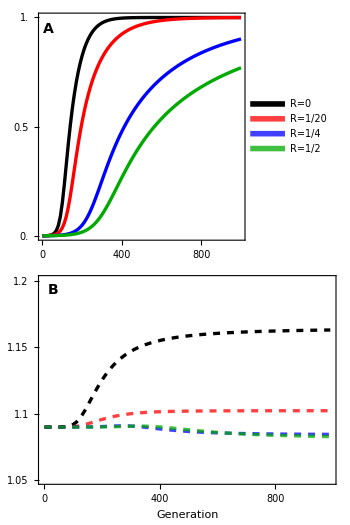

```mathematica
GraphicsColumn[{plot1,plot2},
Spacings->-20,
Epilog->{
},
ImageSize->350
]

Export[plotdir<>"Loose_Fitness_Decline.pdf",%];
```

### Parameters

#### First set of parameters [diploid selection favours A, drive in males favours a]

```mathematica
(*First set of parameters*)
tmax=1000;
tinterval=10;
tplotinterval=200;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];

(*fitness parameters*)
trysAf=0.2;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.2;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.4;
tryFdA=0.5;
tryr=0.05;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

```mathematica
tryRs={0,0.05,0.25,0.45};
tmax=1000;
tmax3=tmax;
tplotinterval=200;
tplotinterval3=tplotinterval;
```

### Plot

#### Y frequency in females

```mathematica
yplotmax=1;
yplotmin=0;

plot1=Legended[
Show[

tryR=tryRs[[1]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Thickness[lwd]]}
],


tryR=tryRs[[3]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Thickness[lwd]]}
],


tryR=tryRs[[4]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Thickness[lwd]]}
],


(*Plot[0.5,{x,0,xplotmax},PlotStyle->{Dashed}],*)

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Y frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.35}
]
];
```

#### Mean diploid fitness

```mathematica
yplotmax=1.151;
yplotmin=1.05;
yplotinterval=0.05;

plot2=(*Legended[*)
Show[

tryR=tryRs[[1]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd],Dashed]}
],

tryR=tryRs[[2]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd],Dashed]}
],

tryR=tryRs[[3]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd],Dashed]}
],


tryR=tryRs[[4]];
(*mean diploid fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd],Dashed]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.75,0.75}
]
]*);
```

#### Combination plot

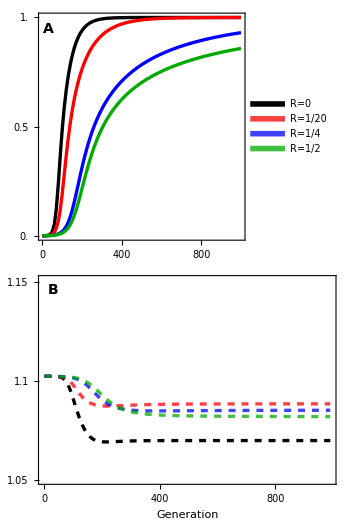

```mathematica
GraphicsColumn[{plot1,plot2},
Spacings->-20,
Epilog->{
},
ImageSize->350
]

(*Export[plotdir<>"Loose_Fitness_Decline.pdf",%];*)
```

## Sex ratio selection is a bad predictor of invasion

### neo-W invasion

#### Parameters

```mathematica
(*plot parameters*)
tmax=1000;
tinterval=10;
tplotinterval=200;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.15,0.5};

(*fitness parameters*)
trysAf=0.2;
tryhAf=0.7;
tryhAm=tryhAf;
trysAm=trysAf;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.4;
tryFdA=0.5;
tryk=1;
tryr=0.05;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;

tryRs={0,0.05,0.25,0.5};
colors={Black,Red,Blue,Darker[Green]};
```

#### Y frequency in females

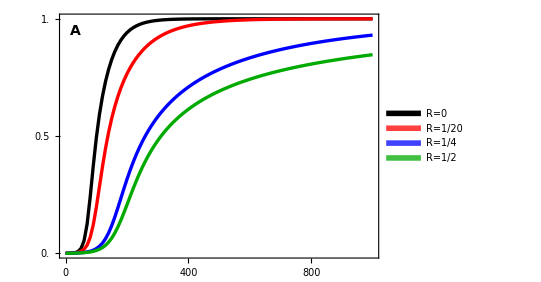

```mathematica
yplotmin=0;
yplotmax=1;

plot1=Legended[
Show[

Table[

tryR=tryRs[[i]];
color=colors[[i]];

(*Y frequency in females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[color,Thickness[lwd]]}
],

{i,1,Length[tryRs]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Y frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.35}
]
]
```

#### Sex ratio

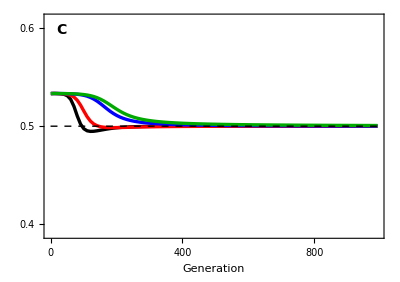

```mathematica
yplotmax=0.61;
yplotmin=0.39;

plot3=
Show[

Table[

tryR=tryRs[[i]];
color=colors[[i]];

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[color,Thickness[lwd]]}
],

{i,1,Length[tryRs]}
],

Plot[0.5,{t,0,tmax},PlotStyle->{Black,Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,Round[yplotmin,0.1],Round[yplotmax,0.1],0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Zygotic sex ratio (fraction male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]
```

### neo-Y invasion

#### Parameters

```mathematica
(*plot parameters*)
tmax=1000;
tinterval=10;
tplotinterval=200;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.1,0.5};

(*fitness parameters*)
trysAf=0.2;
tryhAf=0.7;
tryhAm=tryhAf;
trysAm=trysAf;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.4;
tryk=1;
tryr=0.05;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;

tryRs={0,0.05,0.25,0.5};
colors={Black,Red,Blue,Darker[Green]};
```

#### W frequency in males

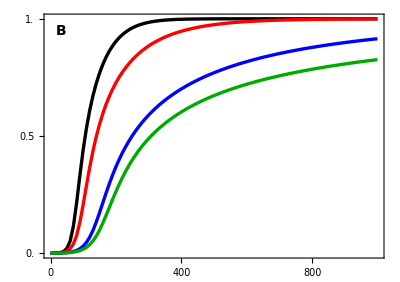

```mathematica
yplotmin=0;
yplotmax=1;

plot2=
Show[

Table[

tryR=tryRs[[i]];
color=colors[[i]];

(*Y frequency in females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[color,Thickness[lwd]]}
],

{i,1,Length[tryRs]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["W frequency in males",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]
```

#### Sex ratio

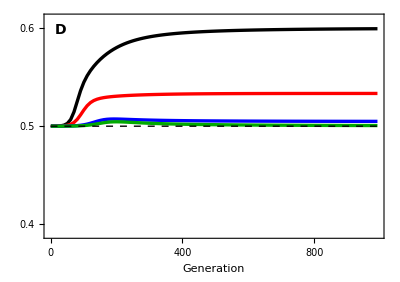

```mathematica
yplotmax=0.61;
yplotmin=0.39;

plot4=
Show[

Table[

tryR=tryRs[[i]];
color=colors[[i]];

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[color,Thickness[lwd]]}
],

{i,1,Length[tryRs]}
],

Plot[0.5,{t,0,tmax},PlotStyle->{Black,Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,Round[yplotmin,0.1],Round[yplotmax,0.1],0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@letpos],
Rotate[Text[Style["",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]
```

### Plot

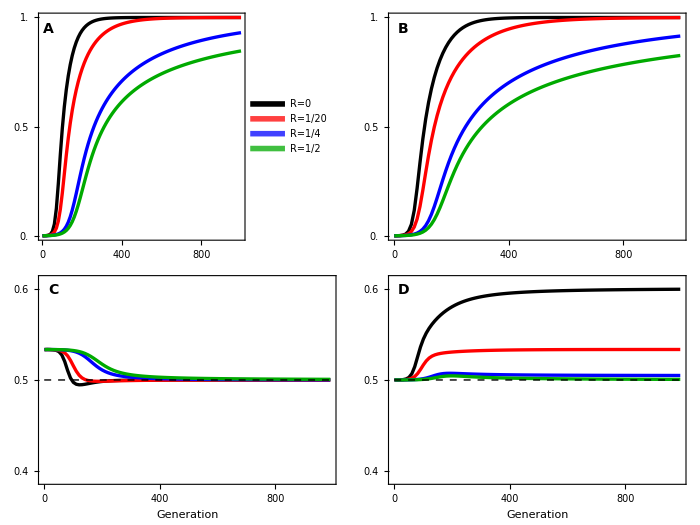

```mathematica
GraphicsGrid[{{plot1,plot2},{plot3,plot4}},
Spacings->-40,
Epilog->{
(*Text[Style["r=0.5, R=0.05",20],Scaled@{0.25,1.45}]*)
},
ImageSize->700
]

Export[plotdir<>"Combination_Turnover_Ratio.pdf",%];
```

## Both neo-W haplotypes can spread in an XY system, without haploid selection, with overdominance

### Parameters

```mathematica
tmax=500;
tinterval=10;
tplotinterval=100;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.175,0.5};

(*fitness parameters*)
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.1;
tryMAa=1;
tryMaa=0.15;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
tryr=0;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];
```

```mathematica
tryR=0;
```

```mathematica
tempeq
```

{0.485714,0.514286,0.238102,0.261898,0.24898,0.25102}

### neo-W frequencies in females

```mathematica
(*The mutant will be introduced at a particular frequency*)
pMA=0.0001;
pMa=0.0001;

trypMXAf=pMA initialpXAf;
trypMXaf=pMa initialpXaf;
trypMXAm=pMA initialpXAm;
trypMXam=pMa initialpXam;
trypMYAf=pMA initialYAf;
trypMYaf=pMa initialYaf;
trypMYAm=pMA initialpYAm;
trypMYam=pMa initialpYam;

yplotmax=0.5;
yplotmin=0;

plotW=
Legended[
Show[

(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Red,Thickness[lwd]]}
],

(*Wa frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Thickness[lwd]]}
],

(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax-tplotinterval,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.25}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["W",14],
Style["WA",14],
Style["Wa",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.75}
]
];
```

### Plot

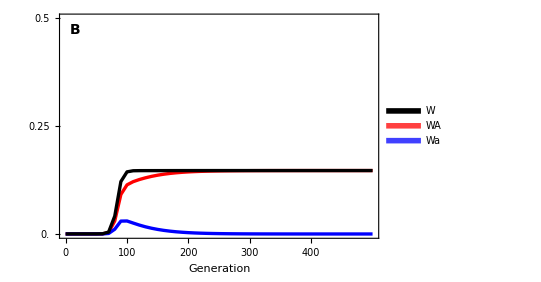

```mathematica
GraphicsColumn[{plotW},
Spacings->0,
ImageSize->300
]

Export[plotdir<>"BothWsInvade_Overdominance.pdf",%];
```

## Both neo-W haplotypes can spread in an XY system, without haploid selection, with overdominance - CYLCES

### Parameters

#### First set of parameters

```mathematica
(*First set of parameters*)
tmax=5000;
tinterval=10;
tplotinterval=1000;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.175,0.5};

(*fitness parameters*)
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.25;
tryMAa=1;
tryMaa=0.25;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
tryr=0.05;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];
```

```mathematica
tryRs={0,0.05,0.25,0.5};
```

### Plot

#### neo-WA frequency in females

```mathematica
(*The mutant will be introduced only on the A haplotype*)
pMA=0.0001;
pMa=0.0001;

trypMXAf=pMA initialpXAf;
trypMXaf=pMa initialpXaf;
trypMXAm=pMA initialpXAm;
trypMXam=pMa initialpXam;
trypMYAf=pMA initialYAf;
trypMYaf=pMa initialYaf;
trypMYAm=pMA initialpYAm;
trypMYam=pMa initialpYam;

yplotmax=0.5;
yplotmin=0;

plotWA=Legended[
Show[

tryR=tryRs[[1]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[3]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[4]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.25}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["neo-WA frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.75}
]
];
```

#### neo-Wa frequency in females

```mathematica
(*The mutant will be introduced only on the a haplotype*)
pMA=0.0001;
pMa=0.0001;

trypMXAf=pMA initialpXAf;
trypMXaf=pMa initialpXaf;
trypMXAm=pMA initialpXAm;
trypMXam=pMa initialpXam;
trypMYAf=pMA initialYAf;
trypMYaf=pMa initialYaf;
trypMYAm=pMA initialpYAm;
trypMYam=pMa initialpYam;

yplotmax=0.5;
yplotmin=0;

plotWa=
Show[

tryR=tryRs[[1]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[3]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[4]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax-tplotinterval,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.25}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["neo-Wa frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
];
```

#### neo-W frequency in females

```mathematica
(*The mutant will be introduced in both haplotypes*)
pMA=0.0001;
pMa=0.0001;

trypMXAf=pMA initialpXAf;
trypMXaf=pMa initialpXaf;
trypMXAm=pMA initialpXAm;
trypMXam=pMa initialpXam;
trypMYAf=pMA initialYAf;
trypMYaf=pMa initialYaf;
trypMYAm=pMA initialpYAm;
trypMYam=pMa initialpYam;

yplotmax=0.5;
yplotmin=0;

plotW=
Show[

tryR=tryRs[[1]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[3]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[4]];
(*WA frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pMA)initialpXAf,(1-pMa)initialpXaf,trypMXAf,trypMXaf,(1-pMA)initialpXAm,(1-pMa)initialpXam,trypMXAm,trypMXam,(1-pMA)initialYAf,(1-pMa)initialYaf,trypMYAf,trypMYaf,(1-pMA)initialpYAm,(1-pMa)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax-tplotinterval,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.25}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["neo-W frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
];
```

#### Combination plot

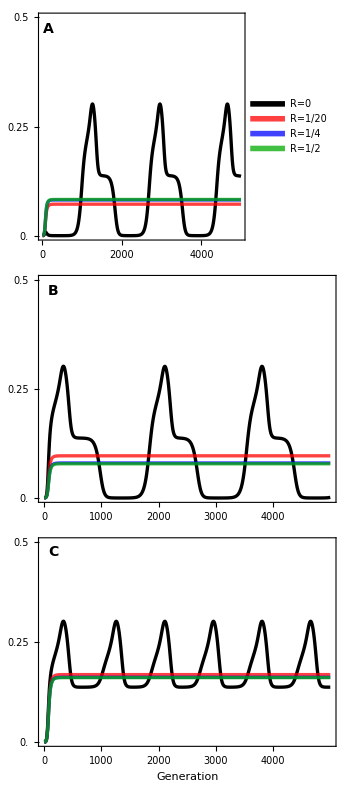

```mathematica
GraphicsColumn[{plotWA,plotWa,plotW},
Spacings->-20,
Epilog->{
},
ImageSize->350
]

Export[plotdir<>"BothWsInvade_Overdominance_Cycles.pdf",%];
```

## Tight linkage and haploid selection can cause stable polymorphic SD systems

### Plot 1

#### First set of parameters

```mathematica
(*First set of parameters*)
tmax=5000;
tinterval=100;
tplotinterval=1000;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.15,0.5};

(*fitness parameters*)
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.1;
tryMAa=1;
tryMaa=0.15;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
tryr=0.1;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;

tryRs={0,0.05,0.25,0.5};
```

#### Y frequency in females

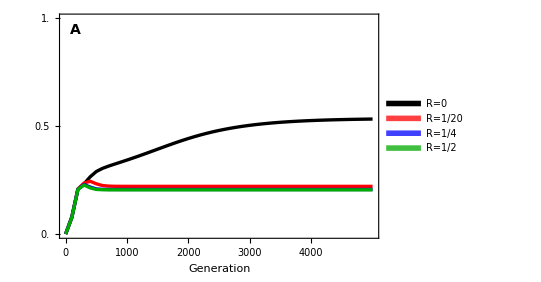

```mathematica
yplotmax=1;
yplotmin=0;

plot1=Legended[
Show[

tryR=tryRs[[1]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Thickness[lwd]]}
],


tryR=tryRs[[3]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Thickness[lwd]]}
],


tryR=tryRs[[4]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Thickness[lwd]]}
],


(*Plot[0.5,{x,0,xplotmax},PlotStyle->{Dashed}],*)

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax-tplotinterval,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Y frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.75}
]
]
```

### Plot 2

#### Second set of parameters

```mathematica
(*First set of parameters*)
tmax=2000;
tinterval=10;
tplotinterval=500;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
xsize=5inches;
aspectratio=1/Sqrt[2];
ylabpos={-0.1,0.5};

(*fitness parameters*)
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.55;
tryr=0.1;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;

tryRs={0,0.05,0.25,0.5};
```

#### Y frequency in females

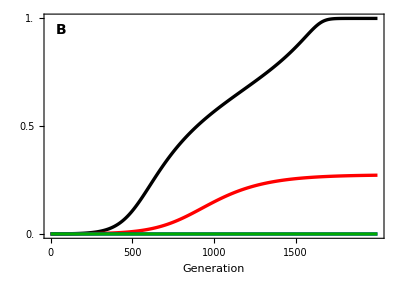

```mathematica
yplotmax=1;
yplotmin=0;

plot2=
(*Legended[*)
Show[

tryR=tryRs[[1]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Thickness[lwd]]}
],


tryR=tryRs[[3]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Thickness[lwd]]}
],


tryR=tryRs[[4]];
(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Thickness[lwd]]}
],


(*Plot[0.5,{x,0,xplotmax},PlotStyle->{Dashed}],*)

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax-tplotinterval,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.3}
]
];*)
```

### Combination plot

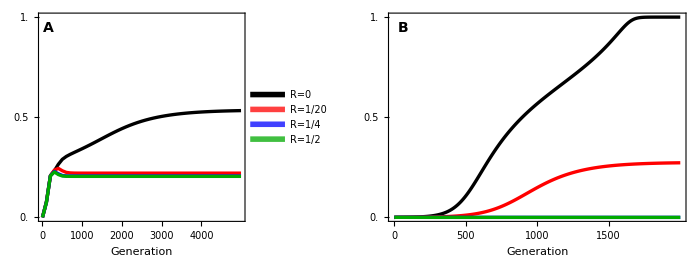

$Aborted

```mathematica
GraphicsRow[{plot1,plot2},
Spacings->-20,
Epilog->{
},
ImageSize->700
]

Export[plotdir<>"Polymorphic.pdf",%];
```